```mathematica
a={{2,-1/2,-1/2},{-1/2,1,-1/2},{-1/2,-1/2,0}};
a=a/3;
MatrixForm[a]
MatrixForm[MatrixPower[a,2]]
MatrixForm[MatrixPower[a,3]]
```

(2/3 | -1/6 | -1/6
-1/6 | 1/3 | -1/6
-1/6 | -1/6 | 0)

(1/2 | -5/36 | -1/12
-5/36 | 1/6 | -1/36
-1/12 | -1/36 | 1/18)

(10/27 | -25/216 | -13/216
-25/216 | 1/12 | -1/216
-13/216 | -1/216 | 1/54)

```mathematica
lsEigenvalue[H_]:=Module[{emax,emaxspace,emin,eminspace,es},(*Find the largest and smallest eigenvalue of a Hermitian matrix H together with the corresponding eigenspace (naive implementation)*)es=Sort[Eigenvalues[H],Re[#1]<Re[#2]&];
emin=First[es];
emax=Last[es];
eminspace=Orthogonalize[NullSpace[H-emin*IdentityMatrix[Length[H]]]];
emaxspace=Orthogonalize[NullSpace[H-emax*IdentityMatrix[Length[H]]]];
Return[{{emin,eminspace},{emax,emaxspace}}]]
plotNR[A_,n_]:=Module[{t=0.,td=2 π/n,Ht,Kt,points={},segments={},emax,emaxspace,emin,eminspace,vp,vm,Q,R},PrintTemporary[ProgressIndicator[Dynamic[t],{0,2 π}]];
(*data for numeric range plot*)While[t<2 π,Ht=(Exp[-I t]*A+Exp[I t]*ConjugateTranspose[A])/2;
{emax,emaxspace}=Last[lsEigenvalue[Ht]];
Which[(*One dimensional eigenspace*)Length[emaxspace]==1,vp=First[emaxspace];
AppendTo[points,Conjugate[vp].A.vp],(*Two or greater dimension-- almost does not happen?*)Length[emaxspace]>1,Kt=(Exp[-I t]*A-Exp[I t]*ConjugateTranspose[A])/(2 I);
Q=Transpose[emaxspace];
R=ConjugateTranspose[Q].Kt.Q;
{{emin,eminspace},{emax,emaxspace}}=lsEigenvalue[R];
vp=Q.First[emaxspace];
vm=Q.First[eminspace];
AppendTo[segments,{Conjugate[vm].A.vm,Conjugate[vp].A.vp}],(*Fail*)True,Print["Error"]];
t=t+td;];
Return[{DeleteDuplicates[points],DeleteDuplicates[segments]}]]
```

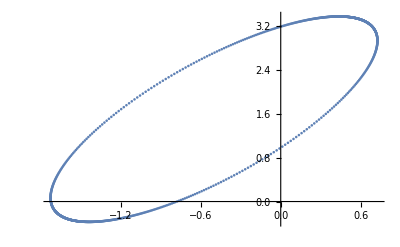

```mathematica
a={{-1,I},{2,3I}};
{nr,dup}=plotNR[a,1000];
ListPlot[nr/.{Complex[x_,y_]->{x,y},x_Real->{x,0}}]
```